## Disk case

#### Disk parameters

```mathematica
mMe= currentfoverv*511/1000*10^-3;(*mirror electron mass in GeV*)mHe=4*mHGeV[currentfoverv];(*mirror Helium mass in GeV*)
QHe=2;(*mirror Helium charge*)nFHe=currentY (3/10)/mHe*5/100(*cm-3*);(*local mirror Helium density*) Reth=64/10*10^8;(*Earth radius in cm. writing all the parameters in rational number helps the calculation precision*)
nEthO=((551/100)/(18/10*10^-24)/16)(*Oxygen number density in cm-3*);
v0He=v0kmsHeDisk[currentfoverv,currentY]*(*(30)**)10^5(*cm/s*); (*velocity deistribution of Helium calulcated in David's code*)

vesc=11*10^5(*cm/s*); (*escape velocity from Earth*)
fvHe[vmin_,vmax_,v0_,vesc_]:=(NIntegrate[√(v^2(*+vesc^2*))*v^2 Exp[-(3 v^2)/(2 v0^2)],{v,vmin,vmax}]/NIntegrate[v^2 Exp[-(3 v^2)/(2 v0^2)],{v,0,10v0}])(*mean velocity of mirror He within cetarin velocity window [vmin, vmax], where v is the particle velocity before falling into the Earth's potential*)
σHe[Q_,v_]:=(4Pi/137^2 QHe^2 Q^2)/(mHe^2(v/(3*10^10))^4)*(2*10^-14)^2(*cm2*)
fHeDisk[v_]:=(correctf[10^-5 v]/.{vescape->vescapehuge, ve->vEarthkmsDisk, v0->v0kmsHeDisk[currentfoverv,currentY]})(* velocity distribution calculated in David's code*)
effσvHe[vmin_,vmax_]:=(NIntegrate[v*σHe[1,v]fHeDisk[v],{v,vmin,vmax}]/NIntegrate[fHeDisk[v],{v,0,10v0He}])(*Eq.(A.9)*)
```

#### Rate calculation

```mathematica
reg=10^-6;

(*Below is the function that calculates the capture rate from soft scattering*)
Rsmallv[ϵ_]:=Module[{vstv,racp},vstv=Abs[vst/.NSolve[(1-vesc^4/vst^4)(vst/(20*10^5))^4 mHe/5(2/QHe)^2(10^-10/ϵ)^2==1,vst][[2]]];(*vst is the v_cap. The expression inside NSolve[] is Eq.(A.5). When the whole expression equals 1, the particle is captured*)
rcap=If[vstv≥vesc,(√(vstv^2-vesc^2))/vesc,0+reg];(*If the v_cap is larger than v_esc, there's a chance to capture the particle since the minimum speed is v_esc. In this case, we define a factor rcap such that the maximum velocity of the particle is rcap*vesc. If v_cap < v_esc, there's no way to catch the particle with soft scattering. We output 0 for the max velocity but put a "regulator" reg to help the numerical integral. The result is insensitive to reg*)

1/Reth*nFHe*SetPrecision[fvHe[SetPrecision[0,50],√((rcap*vesc)^2),v0He,vesc],50](*gives the (number density of He)x(avg flux of He entering the Earth with velocity up to v_cap), which is Eq.(A.6). I kept the maximum precision for all of the numbers since the final calculation is very sentisitive to the accumulated mirror charge.*)
]


(*Below is the function that calculates the capture rate from hard scattering*)
Rlargev[ϵ_]:=Module[{vmin},vmin=SetPrecision[Abs[v/.NSolve[(ϵ^2*σHe[1,v]*nEthO)^-1==Reth,v][[4]]],50];(*Solve the minimum velocity for having scattering length = Earth's redius*)
(*If the hard scattering length is shorter than the Earth radius, the capture is 100% and the capture rate is the 2nd term in the following function. For the 1st term, we only include particle velocity that leads to capture probability < 1, so only a fraction of the mirror He pass through Earth got captured.*)

(nFHe*ϵ^2*SetPrecision[effσvHe[vmin,√(((vesc(mHe+16))/(16-mHe))^2-vesc^2)+reg],50])*nEthO+nFHe*fvHe[0,vmin,v0He,vesc]/Reth
(*The expression of v_max is in the paragraph before the paragraph of Eq.(A.8). Even though Eq.(A.9) in the paper has denominator (v^2+v_esc^2)^2, the way we define the interval in the <σ_HeO v_He> integral cancels the v_esc^2 factor, so the definition should be consistent.*)
]

Rsmallvlist=Table[{-ϵp,Rsmallv[10^-ϵp]},{ϵp,9,12,1/100}];
Rlargevlist=Table[{-ϵp,Rlargev[10^-ϵp]},{ϵp,9,12,1/100}];
(*sumlist=Table[{-ϵp,Rsmallv[10^-ϵp]+Rlargev[10^-ϵp]},{ϵp,9,12,1/100}];*)
```

General::munfl: Exp[-7.5×10^11] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

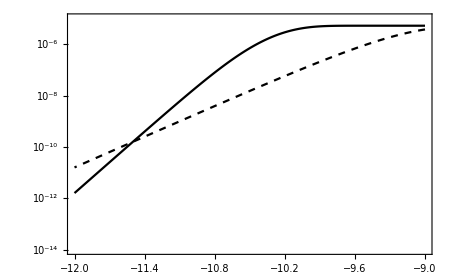

```mathematica
ListLogPlot[{Rsmallvlist,Rlargevlist(*,sumlist*)},PlotStyle-> {Black,{Black,Dashed}},Joined->True,Frame->True(*,FrameLabel->{Style@Text["Log_10 ϵ"],Style@Text["R_(cap,  He)"]}*),LabelStyle->18,ImageSize->450,PlotRange->{{-12,-9},{10^-14,10^-5}}]
```

## Halo case

#### Halo parameters

```mathematica
mMe= currentfoverv*511/1000*10^-3;(*GeV*)mHe=4*mHGeV[currentfoverv];
QHe=2;nFHe=currentY (3/10)/mHe*(5/10)/100(*cm-3*);Reth=64/10*10^8;(*cm*)
nEthO=((551/100)/(18/10*10^-24)/16)(*cm-3*);
v0He=v0kmsHeHalo[currentfoverv,currentY]*(*(30)**)10^5(*cm/s*);

vesc=11*10^5(*cm/s*); (*escape velocity from Earth*)
fvHe[vmin_,vmax_,v0_,vesc_]:=(NIntegrate[√(v^2+vesc^2)*v^2 Exp[-(3 v^2)/(2 v0^2)],{v,vmin,vmax}]/NIntegrate[v^2 Exp[-(3 v^2)/(2 v0^2)],{v,0,10v0}]) (*mean velocity of mirror He within cetarin velocity window [vmin, vmax], where v is the particle velocity before falling into the Earth's potential*)
σHe[Q_,v_]:=(4Pi/137^2 QHe^2 Q^2)/(mHe^2(v/(3*10^10))^4)*(2*10^-14)^2(*cm2*)
fHeHalo[v_]:=(correctf[10^-5 v]/.{vescape->vescapehuge, ve->vEarthkmsHalo, v0->v0kmsHeHalo[currentfoverv,currentY]})
effσvHe[vmin_,vmax_]:=(NIntegrate[v*σHe[1,v]fHeHalo[v],{v,vmin,vmax}]/NIntegrate[fHeHalo[v],{v,0,10v0He}])
```

#### Rate calculation

```mathematica
reg=10^-6;

(*Below is the function that calculates the capture rate from soft scattering*)
Rsmallv[ϵ_]:=Module[{vstv,racp},vstv=Abs[vst/.NSolve[(1-vesc^4/vst^4)(vst/(20*10^5))^4 mHe/5(2/QHe)^2(10^-10/ϵ)^2==1,vst][[2]]];(*vst is the v_cap. The expression inside NSolve[] is Eq.(A.5). When the whole expression equals 1, the particle is captured*)
rcap=If[vstv≥vesc,(√(vstv^2-vesc^2))/vesc,0+reg];(*If the v_cap is larger than v_esc, there's a chance to capture the particle since the minimum speed is v_esc. In this case, we define a factor rcap such that the maximum velocity of the particle is rcap*vesc. If v_cap < v_esc, there's no way to catch the particle with soft scattering. We output 0 for the max velocity but put a "regulator" reg to help the numerical integral. The result is insensitive to reg*)

1/Reth*nFHe*SetPrecision[fvHe[SetPrecision[0,50],√((rcap*vesc)^2),v0He,vesc],50](*gives the (number density of He)x(avg flux of He entering the Earth with velocity up to v_cap), which is Eq.(A.6). I kept the maximum precision for all of the numbers since the final calculation is very sentisitive to the accumulated mirror charge.*)
]


(*Below is the function that calculates the capture rate from hard scattering*)
Rlargev[ϵ_]:=Module[{vmin},vmin=SetPrecision[Abs[v/.NSolve[(ϵ^2*σHe[1,v]*nEthO)^-1==Reth,v][[4]]],50];(*Solve the minimum velocity for having scattering length = Earth's redius*)
(*If the hard scattering length is shorter than the Earth radius, the capture is 100% and the capture rate is the 2nd term in the following function. For the 1st term, we only include particle velocity that leads to capture probability < 1, so only a fraction of the mirror He pass through Earth got captured.*)

(nFHe*ϵ^2*SetPrecision[effσvHe[vmin,√(((vesc(mHe+16))/(16-mHe))^2-vesc^2)+reg],50])*nEthO+nFHe*fvHe[0,vmin,v0He,vesc]/Reth
(*The expression of v_max is in the paragraph before the paragraph of Eq.(A.8). Even though Eq.(A.9) in the paper has denominator (v^2+v_esc^2)^2, the way we define the interval in the <σ_HeO v_He> integral cancels the v_esc^2 factor, so the definition should be consistent.*)
]

Rsmallvlist=Table[{-ϵp,Rsmallv[10^-ϵp]},{ϵp,9,12,1/100}];
Rlargevlist=Table[{-ϵp,Rlargev[10^-ϵp]},{ϵp,9,12,1/100}];
(*sumlist=Table[{-ϵp,Rsmallv[10^-ϵp]+Rlargev[10^-ϵp]},{ϵp,9,12,1/100}];*)
```

General::munfl: Exp[-6.19835×10^9] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

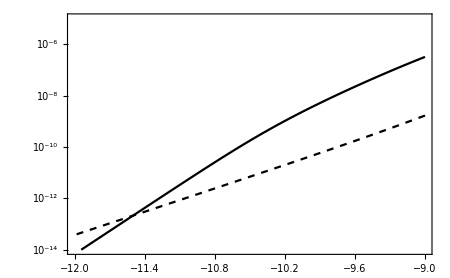

```mathematica
ListLogPlot[{Rsmallvlist,Rlargevlist(*,sumlist*)},PlotStyle-> {Black,{Black,Dashed}},Joined->True,Frame->True(*,FrameLabel->{Style@Text["Log_10 ϵ"],Style@Text["R_(cap,  He)"]}*),LabelStyle->18,ImageSize->450,PlotRange->{{-12,-9},{10^-14,10^-5}}]
```